# Electron cloud propagation

```mathematica
$HistoryLength=0;
<<"NDSolve`FEM`"
SetDirectory[NotebookDirectory[]];

<<"Benchmarking`"
b=Benchmark[];
"BenchmarkResult"/.b[[1]]
```

6.158

## Declaring regions

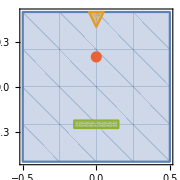

```mathematica
mediumWidth=1.;
mediumHeight=1.;
medium=Region@Rectangle[
{-mediumWidth/2,-mediumHeight/2},
{mediumWidth/2,mediumHeight/2}
];


mediumBM=ToBoundaryMesh@medium;
mediumBE=mediumBM["BoundaryElements"];
needleWidth=0.1;
needleHeight=0.1;
needle=Region@Triangle[{
{-needleWidth/2,mediumHeight/2},
{needleWidth/2,mediumHeight/2},
{0,mediumHeight/2-needleHeight}
}];
needleBM=ToBoundaryMesh@needle;
needleBE=needleBM["BoundaryElements"];


substrateWidth=0.3;
substrateHeight=0.05;
substrate=Region@Rectangle[
{-substrateWidth/2,-mediumHeight/4-substrateHeight/2},
{substrateWidth/2,-mediumHeight/4+substrateHeight/2}
];
substrateBM=ToBoundaryMesh@substrate;
substrateBE=substrateBM["BoundaryElements"];


reg=RegionDifference[medium,substrate~RegionUnion~needle];
nReg=Region@Disk[{0,0.2},0.03];

RegionPlot[{medium,needle,substrate,nReg},ImageSize->Small]
```

## Meshing region

```mathematica
updateElement[prevElementsMesh__,newElement_]:=Module[
{
prevElementsTotalLength=Total[Length[#[[1]]]&/@Flatten@{prevElementsMesh}]
}
,
(Head[#]@@(prevElementsTotalLength+{#[[1]],#[[2]]}))&/@newElement
]

(
bm=ToBoundaryMesh[
"Coordinates"->Join[
mediumBM["Coordinates"],
needleBM["Coordinates"],
substrateBM["Coordinates"]
],
"BoundaryElements"->Join[
mediumBE,
updateElement[mediumBM,needleBE],
updateElement[{mediumBM,needleBM},substrateBE]
],
"RegionHoles"->{{0,-mediumHeight/4},{0,mediumHeight/2}}
]

)["Wireframe"["MeshElementMarkerStyle"->Blue]];

(mesh=ToElementMesh[bm,MaxCellMeasure->10^-4])["Wireframe"];
```

## Resolving electric field

```mathematica
ϕsol=NDSolveValue[
{
Laplacian[ϕ[x,y],{x,y}]==0,
DirichletCondition[ϕ[x,y]==-1,Element[{x,y},RegionBoundary@needle]],
DirichletCondition[ϕ[x,y]==0,Element[{x,y},RegionBoundary@substrate]]
}
,
ϕ,
{x,y}∈mesh
];
ESol= -Grad[ϕsol[x,y],{x,y}];
```

### Some plots

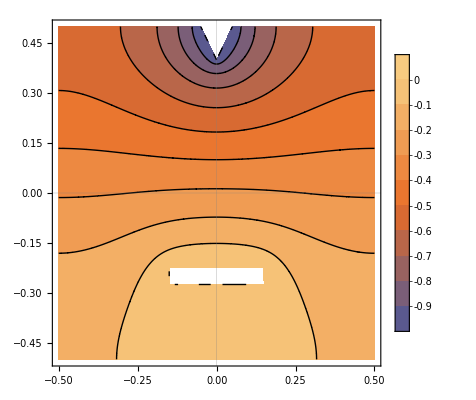

```mathematica
ContourPlot[ϕsol[x,y],{x,y}∈mesh,PlotTheme->"Scientific",PlotLegends->Automatic]
```

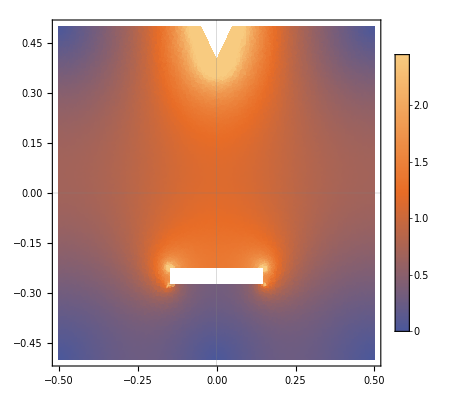

```mathematica
DensityPlot[Norm@ESol,{x,y}∈mesh,PlotTheme->"Scientific",PlotLegends->Automatic,ClippingStyle->Automatic]
```

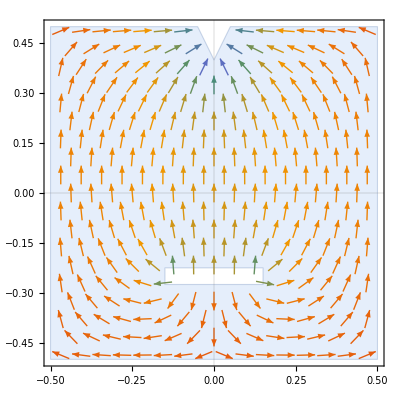

```mathematica
VectorPlot[
ESol,{x,y}∈mesh,
PlotTheme->"Scientific"
]
```

## Resolving cloud motion

```mathematica
f[x_]:=(1.-Exp[-x])/(1.+Exp[-x])
g[x_]:=HeavisideTheta[x-1]f[x-1]
```

### First step

```mathematica
(
nSol=NDSolveValue[
{
D[n[t,x,y],t]+Div[-n[t,x,y]1ESol-0.01Grad[n[t,x,y],{x,y}],{x,y}]== 0Norm[ESol] n[t,x,y]+NeumannValue[10^6 n[t,x,y],{x,y}∈substrate],
n[0,x,y]==0(*If[{x,y}∈nReg,1,0]*),
DirichletCondition[n[t,x,y]==1,{x,y}∈needle],
DirichletCondition[n[t,x,y]==0,{x,y}∈medium]
(*DirichletCondition[n[t,x,y]==0,{x,y}∈substrate],*)
}
,
n,
{t,0,10},
{x,y}∈mesh
]
)//AbsoluteTiming
```

{7.63279,InterpolatingFunction[{{0., 10.}, {-0.5, 0.5}, {-0.5, 0.5}}, <>]}

### Second step

```mathematica
(
nSol=NDSolveValue[
{
D[n[t,x,y],t]+Div[-n[t,x,y]1ESol-0.01Grad[n[t,x,y],{x,y}],{x,y}]==20 Norm[ESol] n[t,x,y]+NeumannValue[10^6 n[t,x,y],{x,y}∈substrate],
n[0,x,y]==If[{x,y}∈nReg,100,nSol[10,x,y]],
DirichletCondition[n[t,x,y]==1,{x,y}∈needle],
DirichletCondition[n[t,x,y]==0,{x,y}∈medium](*,
DirichletCondition[n[t,x,y]==0,{x,y}∈substrate]*)
}
,
n,
{t,0,10},
{x,y}∈mesh
]
)//AbsoluteTiming
```

## Final plotting

### First solution

```mathematica
list=Table[
DensityPlot[
nSol[t,x,y],
{x,y}∈mesh,PlotTheme->"Scientific",PlotLegends->Automatic,ClippingStyle->Automatic,PlotRange->Full
]
,Evaluate[{t,0,tm,tm/50.}/.tm->0.5]
];//EchoTiming

ListAnimate[list]

token="1881814114:AAEyL8EgjrxlDtt-TtO54M9V1zA2ljowxpg";
IdVanya=445281482;
<<"TelegramBotAPI`"
SendMsg[token,IdVanya,"Computation done!"];
```

{11.7753,Null}

{1.26658,Null}

### Coupled solution

```mathematica
list=Table[
DensityPlot[
#[t,x,y],
{x,y}∈medium,PlotTheme->"Scientific",PlotLegends->Automatic,ClippingStyle->Automatic,PlotRange->Full
]&/@sol
,Evaluate[{t,0,tm,tm/50.}/.tm->1]
];//EchoTiming

ListAnimate[list]

token="1881814114:AAEyL8EgjrxlDtt-TtO54M9V1zA2ljowxpg";
IdVanya=445281482;
<<"TelegramBotAPI`"
SendMsg[token,IdVanya,"Computation done!"];
```

3.774

## Coupled solution

### Constants

```mathematica
V=-1;

Subscript[μ, e]=1;
Subscript[d, e]=1;

Subscript[μ, i]=0.1;
Subscript[d, i]=0.1;
```

### Electric field

```mathematica
ϕ[ni_,ne_]:=NDSolveValue[
{
Laplacian[φ[x,y],{x,y}]==4Pi(ni[x,y]-ne[x,y]),
DirichletCondition[φ[x,y]==-1,{x,y}∈needle],
DirichletCondition[φ[x,y]==0,{x,y}∈substrate]
}
,
φ,
{x,y}∈mesh
]
```

```mathematica
m=ϕ[0,0]
```

InterpolatingFunction[{{-0.5, 0.5}, {-0.5, 0.5}}, <>]

```mathematica
Grad[%,{x,y}]
```

{0,0}

```mathematica
ClearAll[ϕ]
```

### Solution

```mathematica
sol=NDSolveValue[
{
(*Poisson*)
Laplacian[ϕ[t,x,y],{x,y}]==(*4Pi(Subscript[n, i][t,x,y]-Subscript[n, e][t,x,y])*)0,
DirichletCondition[ϕ[t,x,y]==V,y>=mediumHeight/2(*{x,y}∈needle*)],
DirichletCondition[ϕ[t,x,y]==0,y<=-mediumHeight/2(*{x,y}∈substrate*)]
(*,

(*Electrons*)
D[Subscript[n, e][t,x,y],t]+Div[-Subscript[n, e][t,x,y] Subscript[μ, e](-Grad[ϕ[t,x,y],{x,y}]),{x,y}]-Subscript[d, e] Laplacian[Subscript[n, e][t,x,y],{x,y}]==0NeumannValue[1,{x,y}∈RegionBoundary@needle],
Subscript[n, e][0,x,y]==0,
DirichletCondition[Subscript[n, e][t,x,y]==0,{x,y}∈needle],
DirichletCondition[Subscript[n, e][t,x,y]==0,{x,y}∈RegionBoundary@medium],
DirichletCondition[Subscript[n, e][t,x,y]==0,{x,y}∈substrate],

(*Ions*)
D[Subscript[n, i][t,x,y],t]+Div[Subscript[n, i][t,x,y] Subscript[μ, i](-Grad[ϕ[t,x,y],{x,y}]),{x,y}]-Subscript[d, i] Laplacian[Subscript[n, i][t,x,y],{x,y}]==0,
Subscript[n, i][0,x,y]==0(*If[{x,y}∈nReg,1,0]*),
DirichletCondition[Subscript[n, i][t,x,y]==0,{x,y}∈needle],
DirichletCondition[Subscript[n, i][t,x,y]==0,{x,y}∈RegionBoundary@medium],
DirichletCondition[Subscript[n, i][t,x,y]==0,{x,y}∈substrate]*)
}
,
{ϕ(*,Subscript[n, e],Subscript[n, i]*)},
{t,0,1},
{x,y}∈mesh
]//EchoTiming
```

NDSolveValue::femnotime: The differential equation cannot be solved as a time dependent equation as specified, most likely because the initial conditions given at (t==0.) are not sufficient to define an initial value problem. As a consequence the differential equation will be solved as a time independent equation.

NDSolveValue::fememrc: The ranges {{0.,1.},ElementMesh[{{-0.5,-0.5},{0.5,-0.5},{0.5,0.5},{-0.5,0.5},{-0.05,0.5},{0.,0.4},{0.05,0.5},{-0.15,-0.275},{0.15,-0.275},{0.15,-0.225},«31379»},{TriangleElement[{{57,24,25,7930,7931,7932},{1134,1141,1111,7933,7934,7935},{3620,3609,3612,7936,7937,7938},{7231,7859,7230,7939,7940,7941},{51,84,73,7942,7943,7944},{1456,1483,1553,7945,7946,7947},{189,183,188,7948,7949,7950},{1632,1539,1635,7951,7952,7953},{1084,1102,531,7954,7955,7956},{61,118,59,7957,7958,7959},«15521»}]},{«1»},{PointElement[{{1},{2},{3},{4},{5},{6},{7},{8},{9},{10},«644»},{12,11,13,14,15,17,16,19,18,20,«644»}]}]} cannot be combined to a region. Please specify a combined region.

0.10604

NDSolveValue[{ϕ^(0,0,2)[t,x,y]+ϕ^(0,2,0)[t,x,y]==0,DirichletCondition[ϕ[t,x,y]==V,y≥0.5],DirichletCondition[ϕ[t,x,y]==0,y≤-0.5]},{ϕ},{t,0,1},{x,y}∈ElementMesh[{{-0.5,0.5},{-0.5,0.5}},{TriangleElement[<15531>]}]]

```mathematica
RegionEmbeddingDimension@RegionDifference[medium,Region@Rectangle[{-0.1,-0.1},{0.1,0.1}]]
```

2

```mathematica
3
```

```mathematica
m=NDSolveValue[
{
Laplacian[ϕ[x,y],{x,y}]==(*4Pi(Subscript[n, i][t,x,y]-Subscript[n, e][t,x,y])*)0,
DirichletCondition[ϕ[x,y]==V,{x,y}∈needle],
DirichletCondition[ϕ[x,y]==0,{x,y}∈substrate]
}
,
ϕ,
{x,y}∈medium
]
```

NDSolveValue::bcnop: No places were found on the boundary where {x,y}∈Region[Rectangle[{-0.15,-0.275},{0.15,-0.225}]] was True, so DirichletCondition[ϕ==0,{x,y}∈Region[Rectangle[{-0.15,-0.275},{0.15,-0.225}]]] will effectively be ignored.

InterpolatingFunction[…]

```mathematica
DensityPlot[#[0.1,x,y],{x,y}∈medium,PlotLegends->Automatic,PlotTheme->"Scientific"]&/@sol//EchoTiming
```

0.072803

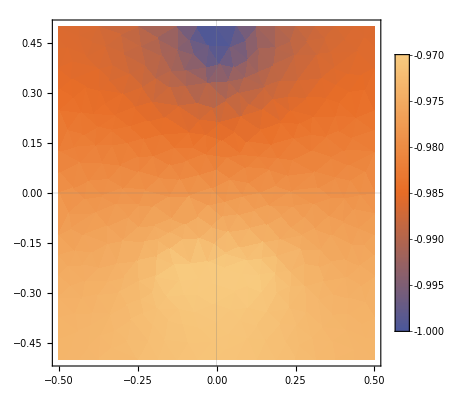

NDSolveValue::fememrc: The ranges {{0.,10.},ElementMesh[{{-0.5,-0.5},{0.5,-0.5},{0.5,0.5},{-0.5,0.5},{-0.05,0.5},{0.,0.4},{0.05,0.5},{-0.15,-0.275},{0.15,-0.275},{0.15,-0.225},«31379»},{TriangleElement[{{57,24,25,7930,7931,7932},{1134,1141,1111,7933,7934,7935},{3620,3609,3612,7936,7937,7938},{7231,7859,7230,7939,7940,7941},{51,84,73,7942,7943,7944},{1456,1483,1553,7945,7946,7947},{189,183,188,7948,7949,7950},{1632,1539,1635,7951,7952,7953},{1084,1102,531,7954,7955,7956},{61,118,59,7957,7958,7959},«15521»}]},{«1»},{PointElement[{{1},{2},{3},{4},{5},{6},{7},{8},{9},{10},«644»},{12,11,13,14,15,17,16,19,18,20,«644»}]}]} cannot be combined to a region. Please specify a combined region.

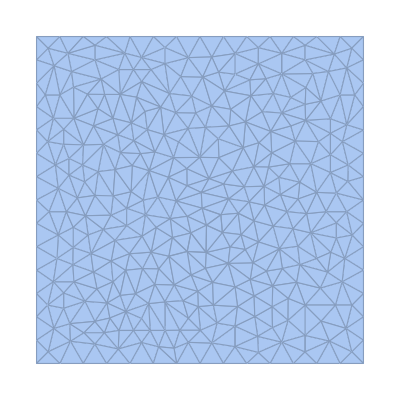

```mathematica
DiscretizeRegion@Region[Rectangle[{-1,-1},{1,1}]]
```

```mathematica
m[x_,y_,z_]:={x,y,z}
```

```mathematica
m[1]
```

m[1]

```mathematica
1/0
```

Power::infy: Infinite expression 1/0 encountered.

ComplexInfinity

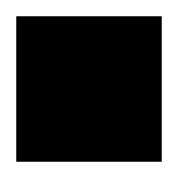

```mathematica
RegionDimension@FullRegion[medium]
```

```mathematica
f@f@a//g
```

g[f[f[a]]]

{"MachineName" -> "8-node homogeneous cluster", "System" -> "MacOSX-ARM64", "BenchmarkName" -> "WolframMark", "FullVersionNumber" -> "12.3.1", 
 "Date" -> "August 2, 2021", "BenchmarkResult" -> 6.726, "TotalTime" -> 49.389}

```mathematica
"BenchmarkResult"/.b[[1]]
```

6.726

```mathematica
BenchmarkReport[]
```

56c0b477-bfc3-4cb7-9238-6a159a06e411WolframMark Report